```mathematica
data=RandomVariate[BernoulliDistribution[0.5],100000];
Mean[data]//N
Variance[data]//N
```

0.49927

0.250002

```mathematica
UnitConvert[Quantity["SpeedOfLight"]/Quantity[970,"Nanometers"]-Quantity["SpeedOfLight"]/Quantity[984,"Nanometers"],"Gigahertz"]//N
```

4397.26 GHz

```mathematica
44*0.8*0.5
```

17.6

```mathematica
((10 10^3)^2)/(100 10^9)//N
```

0.001

```mathematica
10^-5 6 10^3//N
```

0.06

FB

```mathematica
({{iNaCsNR, iCsNR, iNaNR, iEmptyNR}, {iNaCsR, iCsR, iNaR, iEmptyR}})=({{0.7760, 0.1343, 0.0712, 0.0185}, {0.7668, 0.1292, 0.0847, 0.0192}});
({{fNaCsNR, fCsNR, fNaNR, fEmptyNR}, {fNaCsR, fCsR, fNaR, fEmptyR}})=({{0.0221, 0.0323, 0.4079, 0.5377}, {0.1037, 0.0466, 0.4029, 0.4468}})+({{10^-4, 0, 0, 0}, {0, 0, 0, 0}});
NaCsNR=iNaCsNR*m gh-fNaCsNR;
NaCsR=iNaCsR*m (gh+fb)-fNaCsR;
csNR =iCsNR+iNaCsNR(1-m)-fCsNR;
csR = iCsR+iNaCsR(1-m)-fCsR;
naNR = iNaNR-fNaNR;
naR = iNaR-fNaR;
emptyNR = iEmptyNR+iNaCsNR*m*(1-gh)-fEmptyNR;
emptyR = iEmptyR+iNaCsR*m*((1-gh-fb))-fEmptyR;
full=NaCsNR^2+NaCsR^2+csNR^2+csR^2+naNR^2+naR^2+emptyNR^2+emptyR^2;
sol=Minimize[{full,0<=m<=1,0<=fb<=1,0<=gh<=1},{gh,m,fb}]
```

{0.286249,{gh→0.172649,m→0.978252,fb→0.111453}}

```mathematica
sol1
```

{0.286293,{gh→0.172502,m→0.978208,fb→0.11159}}

```mathematica
1/(2 10^-4)({m,gh,fb}/.sol1[[2]])-({m,gh,fb}/.sol2[[2]])
```

{4890.28,863.071,557.156}

```mathematica
{0.2862709771644135,{gh->0.17257556490428436,m->0.9782299876081932,fb->0.11152182609546989}}
```

STIRAP

```mathematica
({{iNaCsNR, iCsNR, iNaNR, iEmptyNR}, {iNaCsR, iCsR, iNaR, iEmptyR}})=({{0.8152, 0.0815, 0.0842, 0.0190}, {0.7745, 0.1304, 0.0788, 0.0163}});
({{fNaCsNR, fCsNR, fNaNR, fEmptyNR}, {fNaCsR, fCsR, fNaR, fEmptyR}})=({{0.0190, 0.0326, 0.4511, 0.4973}, {0.1114, 0.0571, 0.3777, 0.4538}})+({{0, 0, 0, 0}, {0.0, 0, 0, 0}});
(*nacsL=0.603;csL=0.183;naL=0.156;emptyL=0.057;
nacsFr=0.033;nacsFnr=0.0083;csF=0.0155;naF=0.41;emptyFr=0.54;emptyFnr=0.566;*)
nacsL=0.675;csL=0.12;naL=0.171;emptyL=0.033;
nacsFr=0.106;nacsFnr=0.054;csF=0.057;naF=0.422;emptyFr=0.413;emptyFnr=0.463;


NaCsNR=iNaCsNR*m (gh(1-b))-fNaCsNR;
NaCsR=iNaCsR*m (gh(1-b)+fb strp strp)-fNaCsR;
csNR =( iCsNR+iNaCsNR(1-m))(1-b)-fCsNR;
csR =( iCsR+iNaCsR(1-m))(1-b)-fCsR;
naNR = iNaNR+iNaCsNR*m*gh*b-fNaNR;
naR = iNaR+iNaCsR*m*gh*b-fNaR;
emptyNR = iEmptyNR+iCsNR*b+iNaCsNR*m*(1-gh)-fEmptyNR;
emptyR = iEmptyR+iCsR*b+iNaCsR*m*((1-gh-fb)+fb*((1-strp)+strp*(1-strp)))-fEmptyR;
full=NaCsNR^2+NaCsR^2+csNR^2+csR^2+naNR^2+naR^2+emptyNR^2+emptyR^2;

sol=Minimize[{full,0<=m<=1,0<=fb<=1,0<=gh<=1,0<=strp<=1,0<=b<=1},{gh,b,strp,fb,m}]
```

{0.00383633,{gh→0.481704,b→0.898627,strp→0.617383,fb→0.246149,m→0.957164}}

```mathematica
With[{f=m},Normal[Series[full/.f->f0/.sol[[2]],{f0,f/.sol[[2]],2}]]]
```

0.00383633-7.24855×10^-9 (-0.957164+f0)+0.550305 (-0.957164+f0)^2

```mathematica
{0.003980162634465231,{gh->0.48078151698495425,b->0.8950599148552635,strp->0.7184777982940773,fb->0.19500637198953066,m->0.9626057153421714}}
```

```mathematica
NaCsNR^2+NaCsR^2+csNR^2+csR^2+naNR^2+naR^2+emptyNR^2+emptyR^2
```

(-0.0571+(1-b) (0.1304+0.7745 (1-m)))^2+(-0.0326+(1-b) (0.0815+0.8152 (1-m)))^2+(-0.4783+0.0815 b+0.8152 (1-gh) m)^2+(-0.019+0.8152 (1-b) gh m)^2+(-0.2989+0.7745 b gh m)^2+(-0.3669+0.8152 b gh m)^2+(-0.1114+0.7745 m ((1-b) gh+fb strp^2))^2+(-0.4375+0.1304 b+0.7745 m (1-fb-gh+fb (1-strp+(1-strp) strp)))^2

```mathematica
Plot3D[NaCsNR^2+NaCsR^2+csNR^2+csR^2+naNR^2+naR^2+emptyNR^2+emptyR^2/.{gh->test,m->test1}/.{gh->0.4817039828500278,b->0.8986266219269644,strp->0.6173828756427,fb->0.24614893951168498,m->0.9571641681126049},{test,0,1},{test1,0,1}]
```

-Graphics3D-

```mathematica
0.675*0.95*0.21*0.6
```

0.0807975

```mathematica
nacsnr
nacsr
```

-0.0083+0.603 (1-b) ch

-0.033+0.603 ((1-b) ch+fb Abs[strp]^2)

```mathematica
sol
```

{ch→0.459537,b→0.800191,strp→-0.383633,fb→0.462324}

```mathematica
na^2+cs^2+emptyr^2+nacsr^2+nacsnr^2+emptynr^2/.{b->0.98,fb->0.32,ch->0.38,strp->0.7}
```

```mathematica
1/2 UnitConvert[Quantity["SpeedOfLight"]/Quantity[328966,"Gigahertz"]]//N
```

4.55659×10^-7 m

Geometry of the array.

```mathematica
(*arrayGeometry={1,0,1,0,1,0,1,0,1,0,1,0,1,0,1};*)
arrayGeometry={1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1};
arrayPos=Flatten[Position[arrayGeometry,1]];
siteNumber=Length[arrayPos];
```

Statistics of the molecule formation sequence.

```mathematica
atomFilling=0.8;
feshbachFraction=0.3;
unblastedFraction=0.2;
stirapFraction=0.7;
badPrepFraction=0.3;
```

Loading probability per site during the molecule formation sequence.

```mathematica
stats:=Module[{},fillingA=ConstantArray[0,nTrials];
Do[
csLoading=RandomVariate[BernoulliDistribution[atomFilling],siteNumber];
naLoading=RandomVariate[BernoulliDistribution[atomFilling],siteNumber];
pairLoading=Times@@{csLoading,naLoading}ᵀ;
fbStep=pairLoading*RandomChoice[{feshbachFraction,1-feshbachFraction-badPrepFraction,badPrepFraction}->{fb,gh,bh},8]; (*feshbach, good hyperfine, bad hyperfine*)
fbLoading=fbStep/.{fb->1,gh->0,bh->0};
ghLoading=fbStep/.{fb->0,gh->1,bh->0};
ghubLoading=ghLoading*RandomVariate[BernoulliDistribution[unblastedFraction],siteNumber];
gsLoading=fbLoading*RandomVariate[BernoulliDistribution[stirapFraction],siteNumber];
imageLoading=gsLoading*RandomVariate[BernoulliDistribution[stirapFraction],siteNumber]+ghubLoading;

fillingA[[trial]]=N[Mean[imageLoading]]; (*replace the argument of 'Mean' to calculate loading of other species in the sequence*)
,{trial,1,nTrials}];
Mean[fillingA]];
```

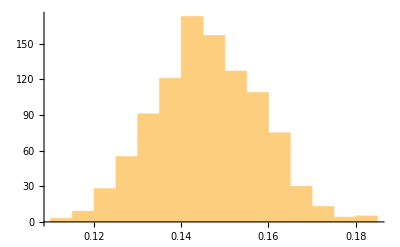

```mathematica
Histogram[Table[stats,{n,1,1000}]]
```

Setup the single particle Hilbert space,  operators, matrix elements, and parameters.

```mathematica
nℋ1=2;
ℋ1=IdentityMatrix[nℋ1];
sℋ1=Partition[ℋ1,{nℋ1,1}]⟦1⟧;
lℋ1=Range[0,nℋ1-1];
s2lℋ1=AssociationThread[sℋ1->lℋ1];
l2sℋ1=AssociationThread[lℋ1->sℋ1];
σx=PauliMatrix[1];σy=PauliMatrix[2];σz=PauliMatrix[3];σp=1/2 (σx+ⅈ σy);σm=1/2 (σx-ⅈ σy);id=IdentityMatrix[2];σn=Cos[θ] σx+Sin[θ] σy;
(*arrayGeometry={1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1};*)
ddℋn[{site1_,site2_,distance_}]:=1/distance^3(KroneckerProduct@@(ReplacePart[idArray,{site1->σp,site2->σm}])+KroneckerProduct@@(ReplacePart[idArray,{site1->σm,site2->σp}]));
fillingFraction=0.15;
tRange=Range[0,20000,500];
nTrials=100;
```

Calculate site filling of an array of molecules after a Ramsey pulse and with the dipolar interaction.

```mathematica
findFilling[t_]:=Module[{},
siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];
(*wi=0;
While[siteFilling[[1;;2]]!={1,1},siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];wi++];*)
sitePos=Flatten[Position[siteFilling,1]];
nP=Length[sitePos];
siteDistances=Select[Flatten[Table[{i,j,5(arrayPos[[sitePos[[j]]]]-arrayPos[[sitePos[[i]]]])},{i,Range[nP]},{j,Range[nP]}],1],#[[3]]>0&];
If[nP<=1,finalFilling=siteFilling*RandomVariate[BernoulliDistribution[stirapFraction],siteNumber];,
nℋn=nℋ1^nP;
lℋn=Tuples[lℋ1,nP];
ℋn=IdentityMatrix[nℋn];
sℋn=Partition[ℋn,{nℋn,1}][[1]];
s2lℋn=AssociationThread[sℋn->lℋn];
l2sℋn=AssociationThread[lℋn->sℋn];
idArray=ConstantArray[id,nP];
σxℋn=Sum[KroneckerProduct@@ReplacePart[idArray,p->σx/2],{p,1,nP}];
numℋn[p_]:=KroneckerProduct@@ReplacePart[idArray,p->σp.σm];
σnℋn=Sum[KroneckerProduct@@ReplacePart[idArray,p->σn/2],{p,1,nP}];
numAvgℋn=Sum[numℋn[p]/nP,{p,1,nP}];
idℋn=KroneckerProduct@@idArray;
ψ0=KroneckerProduct@@ConstantArray[l2sℋ1[0],nP];
op1=N[σxℋn];
op2=N[idℋn+Total[ddℋn[#]&/@siteDistances]];
ψ=MatrixExp[ⅈ op1 π/2].MatrixExp[-ⅈ op2 t].MatrixExp[-ⅈ op1 π/2].ψ0;
nBySite=Table[Re[N[ψ†.numℋn[p].ψ]][[1,1]],{p,1,nP}];
finalFilling=imageEff*ReplacePart[siteFilling,Table[sitePos[[p]]->RandomVariate[BernoulliDistribution[nBySite[[p]]]],{p,1,nP}]]+RandomVariate[BernoulliDistribution[0.05],siteNumber];
];
N[finalFilling]
]
```

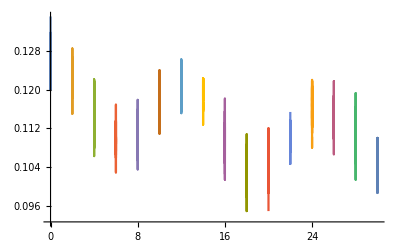

```mathematica
ListPlot[Table[{t 4/2000,Mean[ParallelTable[Mean[findFilling[t]],{n,1,1000}]]},{t,0,15000,1000},{trial,1,20}],Joined->True]
```

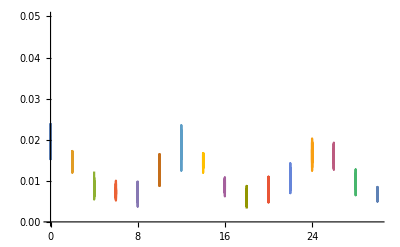

```mathematica
ListPlot[Table[{t 4/2000,Mean[ParallelTable[Mean[Times@@@ArrayReshape[findFilling[t],{4,2}]],{n,1,1000}]]},{t,0,15000,1000},{trial,1,20}],Joined->True,PlotRange->{0,0.05}]
```

```mathematica
pairs[f_]:={f[[1]]f[[2]],f[[2]]f[[3]],f[[3]]f[[4]],f[[4]]f[[5]],f[[5]]f[[6]],f[[6]]f[[7]],f[[7]]f[[8]]}
```

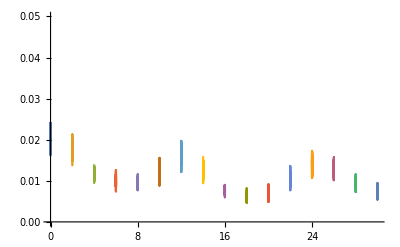

```mathematica
ListPlot[Table[{t 4/2000,Mean[ParallelTable[Mean[pairs[findFilling[t]]],{n,1,1000}]]},{t,0,15000,1000},{trial,1,20}],Joined->True,PlotRange->{0,0.05}]
```

```mathematica
0.57*.17
```

0.0969

```mathematica
0.71*0.78*0.09+0.03+0.71*0.78*0.31
```

0.25152

```mathematica
Solve[0.71*0.78*0.09+0.03==0.097,x]
```

{}

```mathematica
0.57*0.83*0.58
```

0.274398

```mathematica
1-0.21*2
```

0.58

```mathematica
0.15+0.71
```